# Read Perturbed QNM

```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[]
```

/Users/rodrigopanossomacedo/Trabalhos/QMUL/QNM_PseudoSpectra/Notebook/Schwarzschild

## Simulation Parameters

```mathematica
spin=-2;
l=2;
ϵ=10^(-8);
FuncName="NoFunc";
kk=60;
Prec=500;

NzMin=350;
NzMax=400;
ΔNz=50;
```

### Set Files With Physical Configuration

```mathematica
Nz=Table[ir,{ir,NzMin,NzMax, ΔNz}];
ResLength=Length@Nz;

fn=Table["Data/Spectra_spin_"<>ToString[spin]<>"_l_"<>ToString[l]<>"_"<>FuncName<>"FreqPert_eps_"<>ToString[AccountingForm[N@ϵ]]<>"_ksig_"<>ToString[N[kk]]<>"_N_"<>ToString[Nz[[i]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat",{i,1,ResLength}]
```

{Data/Spectra_spin_-2_l_2_NoFuncFreqPert_eps_0.00000001_ksig_60._N_350_Prec_500.dat,Data/Spectra_spin_-2_l_2_NoFuncFreqPert_eps_0.00000001_ksig_60._N_400_Prec_500.dat}

### Read Data

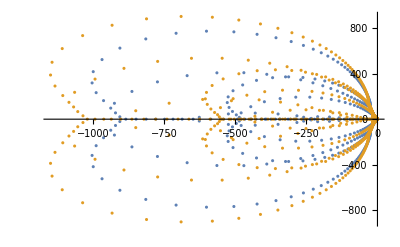

```mathematica
SpectraRead=Table[ Import[fn[[i]], "Table"],{i,1,ResLength}];

ListPlot[SpectraRead, PlotRange->Full]
```

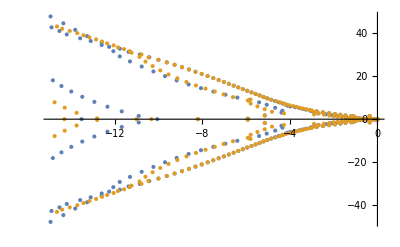

```mathematica
Res=-15;
SpectraFilter=Table[DeleteCases[SpectraRead[[i]],x_/;x[[1]]≤Res],{i,1,ResLength}];
ListPlot[SpectraFilter]
```

```mathematica
QNM =Table[DeleteCases[SpectraRead[[i]],x_/;x[[2]]==0],{i,1,ResLength}];
BranchCut=Table[DeleteCases[SpectraRead[[i]],x_/;x[[2]]!=0],{i,1,ResLength}];

NQNMHigh=Length@QNM[[ResLength]];
NQNMLow=Length@QNM[[ResLength-1]];
NQNM=Min[NQNMHigh,NQNMLow];

NBranchCutHigh=Length@BranchCut[[ResLength]];
NBranchCutLow=Length@BranchCut[[ResLength-1]];
NBranchCut=Min[NBranchCutHigh,NBranchCutLow];


QNMLow=If[NQNMLow==NQNM,
QNM[[1]],
Drop[QNM[[1]],NQNM-NQNMLow]
];

QNMHigh=If[NQNMHigh==NQNM,
QNM[[2]],
Drop[QNM[[2]],NQNM-NQNMHigh]
];
```

### Find Converging values by looking at the intersection of results with different resolutions

87

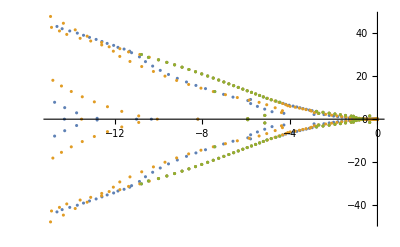

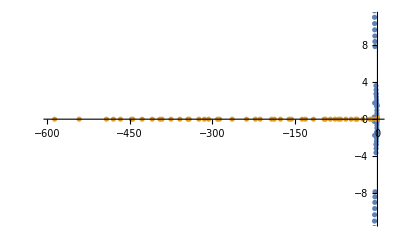

```mathematica
TINY=10^(-1);
QNMIntersection=Intersection[ 
QNM[[ResLength]],
QNM[[ResLength-1]],
SameTest->(Total@Abs[#1-#2]<TINY &)
];
Length@QNMIntersection
ListPlot[{SpectraFilter[[ResLength]],SpectraFilter[[ResLength-1]],QNMIntersection}]
ListPlot[{QNMIntersection,BranchCut[[1]]}]
```

```mathematica
fn="Data/CleanQNM_spin_"<>ToString[spin]<>"_l_"<>ToString[l]<>"_"<>FuncName<>"FreqPert_eps_"<>ToString[AccountingForm@N[ϵ]]<>"_ksig_"<>ToString[N[kk]]<>"_N_"<>ToString[Nz[[1]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
Export[fn,QNMIntersection,"Table"]

fn="Data/CleanBranchCut_spin_"<>ToString[spin]<>"_l_"<>ToString[l]<>"_"<>FuncName<>"FreqPert_eps_"<>ToString[AccountingForm@N[ϵ]]<>"_ksig_"<>ToString[N[kk]]<>"_N_"<>ToString[Nz[[1]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
Export[fn,BranchCut[[1]],"Table"]
```

Data/CleanQNM_spin_-2_l_2_NoFuncFreqPert_eps_0.00000001_ksig_60._N_350_Prec_500.dat

Data/CleanBranchCut_spin_-2_l_2_NoFuncFreqPert_eps_0.00000001_ksig_60._N_350_Prec_500.dat